```mathematica
m = ({{1, 0, 0, 0, 1}, {1, 0, 0, 0, 1}, {1, 1, 0, 0, 2}, {1, 1, 1, 0, 2}, {0, 1, 1, 1, 2}, {0, 0, 1, 1, 1}})
n=({{1, 1}, {-1, 2}, {-1, 2}, {-1, 2}, {-1, 1}})
```

{{1,0,0,0,1},{1,0,0,0,1},{1,1,0,0,2},{1,1,1,0,2},{0,1,1,1,2},{0,0,1,1,1}}

{{1,1},{-1,2},{-1,2},{-1,2},{-1,1}}

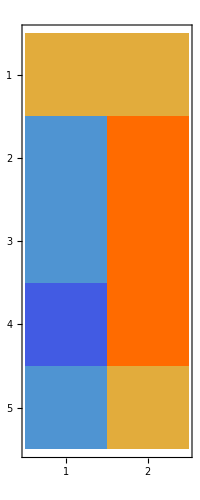

```mathematica
MatrixPlot[n=({{1, 1}, {-1, 2}, {-1, 2}, {-2, 2}, {-1, 1}})]
```

```mathematica
RowReduce[m]
```

{{1,0,0,0,1},{0,1,0,0,1},{0,0,1,0,0},{0,0,0,1,1},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
MatrixForm[%]
```

(1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
({{1, 0, 0, 0, 1}, {0, 1, 0, 0, 1}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 1}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}})
```

```mathematica
(18*32)/3
```

192

```mathematica
a = ({{1, 1, 0, 0, 0}, {1, 1, 1, 0, 0}, {0, 1, 1, 1, 0}, {0, 0, 1, 1, 1}, {0, 0, 0, 1, 1}});
b=({{1}, {2}, {2}, {2}, {1}});
LinearSolve[a,b]
```

{{1},{0},{1},{1},{0}}